=== TCCT Topological NAND Gate (Perfect Isolation) ===

Input (A:0, B:0) -> Output C: 1

Input (A:0, B:1) -> Output C: 1

Input (A:1, B:0) -> Output C: 1

Input (A:1, B:1) -> Output C: 0

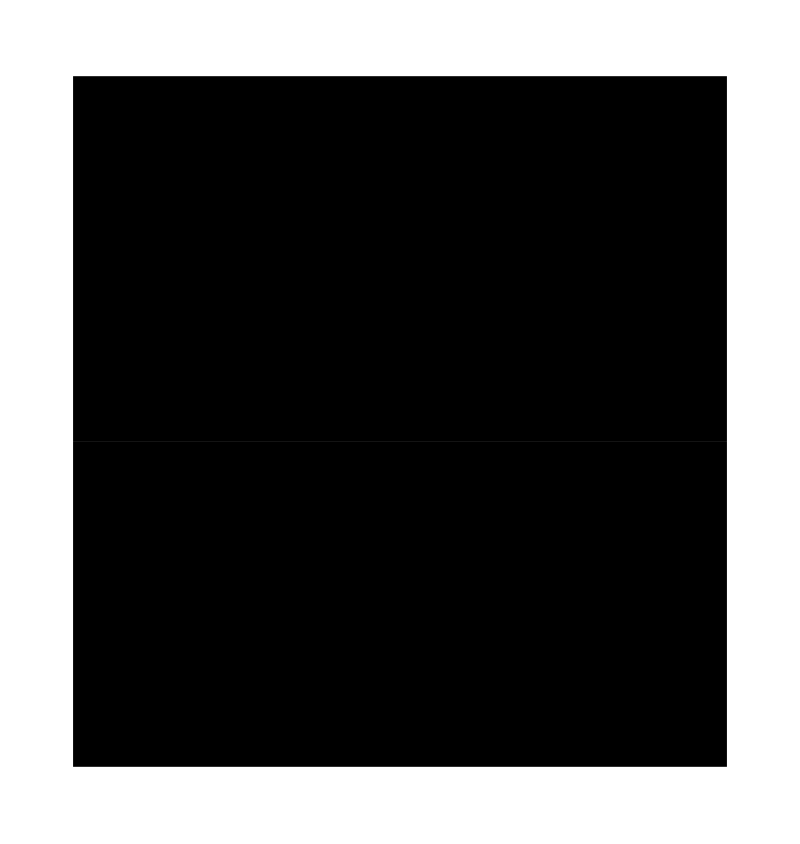

```mathematica
ClearAll["Global`*"];
SeedRandom[];

(* ==========================================================*)
(*1. 真空脚手架：引入双探测器 C1,C2 彻底解决点级拓扑短路*)
(* ==========================================================*)
nandNodes={"V1","V2","A","B","M1","M2","C1","C2"};

(*基底边缘序列依然保持严格的 LIFO 拓扑拦截顺序*)
baseEdges={UndirectedEdge["M1","C1"],UndirectedEdge["V1","M1"],UndirectedEdge["M2","C2"],UndirectedEdge["V2","M2"]};

vacuumGraph=Graph[nandNodes,baseEdges,VertexLabels->Placed["Name",Center],VertexSize->0.4,GraphLayout->"SpringEmbedding"];

InjectNAND[inputA_,inputB_]:=Module[{g=vacuumGraph},If[inputA==1,g=EdgeAdd[g,UndirectedEdge["A","M1"]]];
If[inputB==1,g=EdgeAdd[g,UndirectedEdge["B","M2"]]];
Return[g];]

(* ==========================================================*)
(*2. 并发暴胀引擎 (Window Parallel+Chronological Wavefront)*)
(* ==========================================================*)
StepEvolutionParallel[g_Graph,window_]:=Module[{allEdges,activeEdges,nActive,usedEdges,updates,tempE1,tempE2,x,y,z,wCounter,newVertices,newActive,newFrozen,remainingEdges,intNodes},allEdges=EdgeList[g];
(*LIFO 逆向因果波前：最新扰动优先享有最高干涉权*)activeEdges=Reverse[Cases[allEdges,_UndirectedEdge]];
nActive=Length[activeEdges];
If[nActive<2,Return[g]];
usedEdges={};updates={};
Do[tempE1=activeEdges[[i]];
If[!MemberQ[usedEdges,tempE1],Do[tempE2=activeEdges[[j]];
If[!MemberQ[usedEdges,tempE2]&&Length[Intersection[List@@tempE1,List@@tempE2]]==1,AppendTo[updates,{tempE1,tempE2}];
AppendTo[usedEdges,tempE1];
AppendTo[usedEdges,tempE2];
Break[];],{j,i+1,Min[i+window,nActive]}]],{i,1,nActive}];
If[Length[updates]==0,Return[g]];
intNodes=Cases[VertexList[g],_Integer];
wCounter=If[Length[intNodes]==0,1,Max[intNodes]];
newVertices={};newActive={};newFrozen={};
Do[y=Intersection[List@@pair[[1]],List@@pair[[2]]][[1]];
x=Complement[List@@pair[[1]],{y}][[1]];
z=Complement[List@@pair[[2]],{y}][[1]];
wCounter++;
AppendTo[newVertices,wCounter];
newActive=Join[newActive,{UndirectedEdge[x,z],UndirectedEdge[x,wCounter],UndirectedEdge[wCounter,z]}];
newFrozen=Join[newFrozen,{DirectedEdge[x,y],DirectedEdge[y,z]}];,{pair,updates}];
remainingEdges=Complement[allEdges,Flatten[updates]];
Graph[Union[Join[VertexList[g],newVertices]],Union[Join[remainingEdges,newActive,newFrozen]],VertexLabels->Placed["Name",Center],VertexSize->0.4,EdgeStyle->{_UndirectedEdge->Directive[Cyan,Thick],_DirectedEdge->Directive[Gray,Thin]},Background->Black]]

(* ==========================================================*)
(*3. 宏观体积测量算符*)
(* ==========================================================*)
MeasureOutput[finalGraph_]:=Module[{finalEdges,activeToC},finalEdges=EdgeList[finalGraph];
(*物理测量法则：检查 C1 或 C2 是否接收到了全新的活性因果连接*)activeToC=Cases[finalEdges,UndirectedEdge["C1",n_]/;n=!="M1"]~Join~Cases[finalEdges,UndirectedEdge[n_,"C1"]/;n=!="M1"]~Join~Cases[finalEdges,UndirectedEdge["C2",n_]/;n=!="M2"]~Join~Cases[finalEdges,UndirectedEdge[n_,"C2"]/;n=!="M2"];
If[Length[activeToC]>0,1,0]]

RunNANDTest[inputA_,inputB_,window_,steps_]:=Module[{g=InjectNAND[inputA,inputB],i},Do[g=StepEvolutionParallel[g,window],{i,1,steps}];
Return[g];]

(* ==========================================================*)
(*4. 终极真值表盲测与流形渲染*)
(* ==========================================================*)
Print[Style["=== TCCT Topological NAND Gate (Perfect Isolation) ===",White,Bold,16,Background->Black]];
testCases={{0,0},{0,1},{1,0},{1,1}};
results={};graphs={};

Do[inA=testCases[[i,1]];inB=testCases[[i,2]];
(*并发火力全开 (window=10)，2 步演化足以完成空间切割*)finalG=RunNANDTest[inA,inB,10,2];
outC=MeasureOutput[finalG];
AppendTo[results,{inA,inB,outC}];
AppendTo[graphs,finalG];
Print[Style[StringForm["Input (A:``, B:``) -> Output C: ``",inA,inB,outC],14,Bold,If[outC==1,Green,Red]]];,{i,1,4}];

Print[GraphicsGrid[Partition[MapThread[Labeled[#1,Style[StringForm["(A:``, B:``) -> Output: ``",#2[[1]],#2[[2]],#2[[3]]],14,Bold,White]]&,{graphs,results}],2],ImageSize->800,Background->Black]]
```